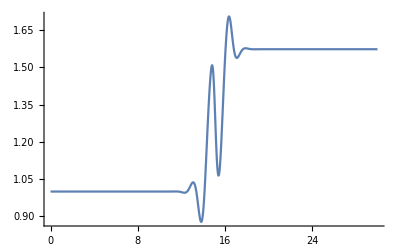

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(π/2) Erf[10499571/(700000 √2)]+√(π/2) Erf[15/(√2)].

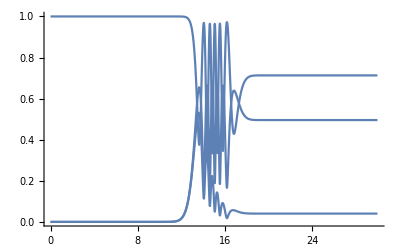

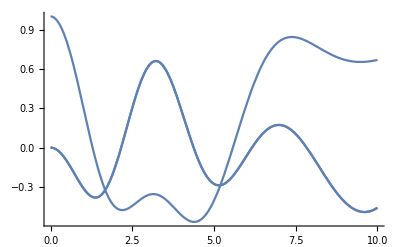

```mathematica
Clear[Ω,Ω0]
k=0.0;
x0=15;
σ=1;
Ω0=1;
Ω[x_]:=Ω0*Exp[-(x-x0)^2/(2*σ^2)];
Gsol=NDSolve[{G'[t]-I/2*G[t]^2*Ω[t]*Exp[-4*I*t]==Ω[t]*Exp[4*I*t],G[0]==1},{G[t]},{t,0,tf}];
Plot[Re[Evaluate[{G[t]}/.Gsol]],{t,0,tf},PlotRange->All]


tf=30;
Cf[Ω0_]:=Module[{y},
Ω[x_]:=Ω0*Exp[-(x-x0)^2/(2*σ^2)];
sol=NDSolve[{I*Cm1'[t]==Ω[t]/2*C0[t]+(1-k)*Cm1[t],I*C1'[t]==Ω[t]/2*C0[t]+(1+k)*C1[t],I*C0'[t]==Ω[t]/2*(C1[t]+Cm1[t]),C0[0]==1,C1[0]==0,Cm1[0]==0},{C1[t],Cm1[t],C0[t]},{t,0,tf}];
y=C1[t]/.sol[[1]]/.t->tf]

Plot[Re[Evaluate[{Exp[-Integrate[Ω[x],{x,0,t}]]Abs[C1[t]],Abs[C0[t]],Abs[Cm1[t]]}/.sol]],{t,0,tf},PlotRange->All]
```

```mathematica
s=DSolve[{I*Cp'[t]==Ω[t]/Sqrt[2]*C0[t]+2*Cp[t],I*C0'[t]==-2*C0[t]+Ω[t]/Sqrt[2]*Cp[t],C0[0]==1,Cp[0]==0},{Cp[t],C0[t]},t]
```

DSolve[{ⅈ Cp'[t]==(ⅇ^(-t^2/2) C0[t])/(√2)+2 Cp[t],ⅈ C0'[t]==-2 C0[t]+(ⅇ^(-t^2/2) Cp[t])/(√2),C0[0]==1,Cp[0]==0},{Cp[t],C0[t]},t]

```mathematica
C1[t]/.sol[[1]]/.t->10
```

-3.1243×10^-7-1.02058×10^-6 ⅈ

```mathematica
sol[[1]][[1]]
Re[0.3*Exp[-I*t]*Exp[0.3*Ω[t]]]
Re[0.3*Exp[-I*t]*Exp[0.3*Ω[t]]],Re[C1[t]],Re[C0[t]],Re[Cm1[t]]}/.sol
```

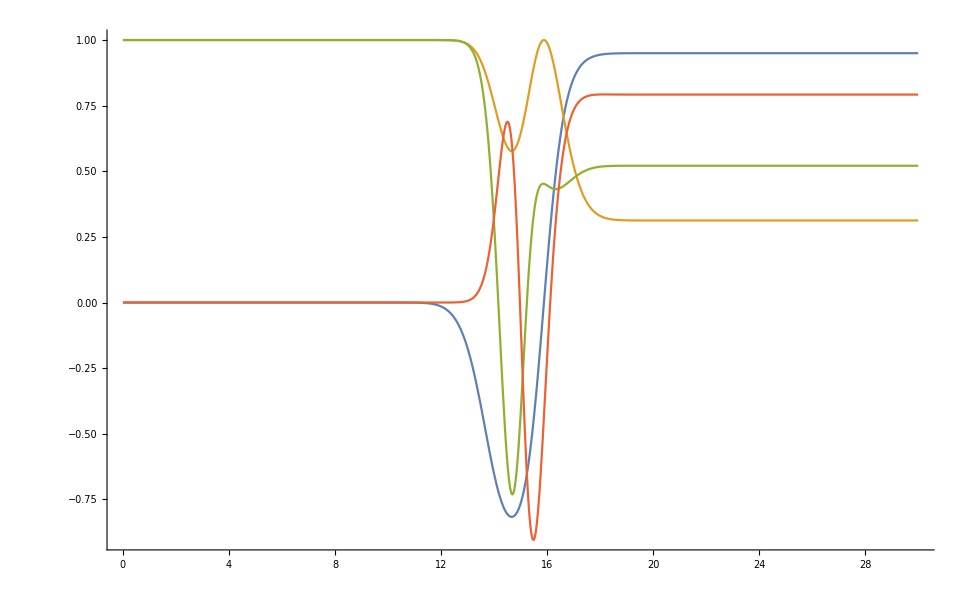

```mathematica
a=0.1;
b=-0.3;
Plot[Evaluate[{Im[Exp[a*I*Integrate[Ω[x],{x,0,t}]]*Exp[I*b*Ω[t]]],Re[Exp[a*I*Integrate[Ω[x],{x,0,t}]]*Exp[I*b*Ω[t]]],Re[C0[t]],Im[C0[t]]}/.sol],{t,0,tf},PlotRange->All]
```

```mathematica
ω=1;
a=1;
DSolve[{C1''[t]+(2*a*t+4*ω*I)*C1'[t]+(Ω[t]^2/2+8*I*ω*a*t)*C1[t]==0,C1[0]==0},{C1[t]},t]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

DSolve[{(12.4914 ⅇ^(-(-15+t)^2)+8 ⅈ t) C1[t]+(4 ⅈ+2 t) C1'[t]+C1''[t]==0,C1[0]==0},{C1[t]},t]

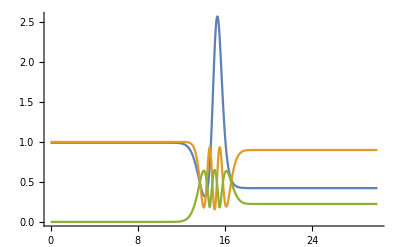

```mathematica
Plot[Evaluate[{(Exp[0.01334*Integrate[Ω[x],{x,0,t}]]*(0.99515-0.450986*Im[Exp[0.6143*I*Integrate[Ω[x],{x,0,t}]]]))^2,Abs[C0[t]]^2,Abs[C1[t]]}/.sol],{t,0,tf},PlotRange->All]
```

```mathematica
line=Fit[Evaluate[Abs[C0[2]]/.sol],{1,x},x]
```

0.5 Abs[C0[2]]+0.5 x Abs[C0[2]]

```mathematica
fun=C0[t]/.sol[[1]][[3]];
data=Table[{t,Abs[fun]^2},{t,0,30,0.01}];
```

```mathematica
data={t,Abs[fun]}/.t->Range[0,tf,1]
data1=Abs[fun]/.t->Range[0,tf,1];
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999933,0.981904,0.442391,0.435208,0.49469,0.872268,0.946601,0.948281,0.94824,0.948239,0.948239,0.948239,0.948239,0.948239,0.948239,0.948239,0.948239,0.948239,0.948239}}

```mathematica
line=Fit[data,{1,x},x]
```

0.978882-0.00263288 x

2.99897 ⅇ^(-1/2 (-15+x)^2)

ⅇ^(a1 (3.75865+3.75865 Erf[(-15+t)/(√2)])) Re[ⅇ^(ⅈ a1 b1 t (3.75865+3.75865 Erf[(-15+t)/(√2)]))]

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a1→0.000282732,b1→226.348,b2→1.,c1→1.}

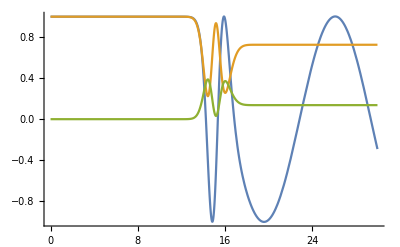

```mathematica
Ω[x]
model=Exp[Integrate[a1*Ω[x],{x,0,t}]]*Re[Exp[Integrate[a1*Ω[x]*t,{x,0,t}]*b1*I]]
fit=FindFit[data,model,{a1,b1,b2,c1},t]
Plot[Evaluate[{model/.fit,Abs[C0[t]]^2,Abs[C1[t]]^2}/.sol],{t,0,tf},PlotRange->All]
```

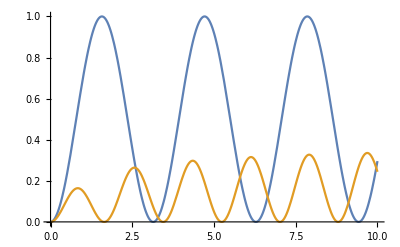

```mathematica
Plot[{Sin[x]^2*Exp[Intergate[]],Abs[Cf[x]]^2},{x,0,10}]
```

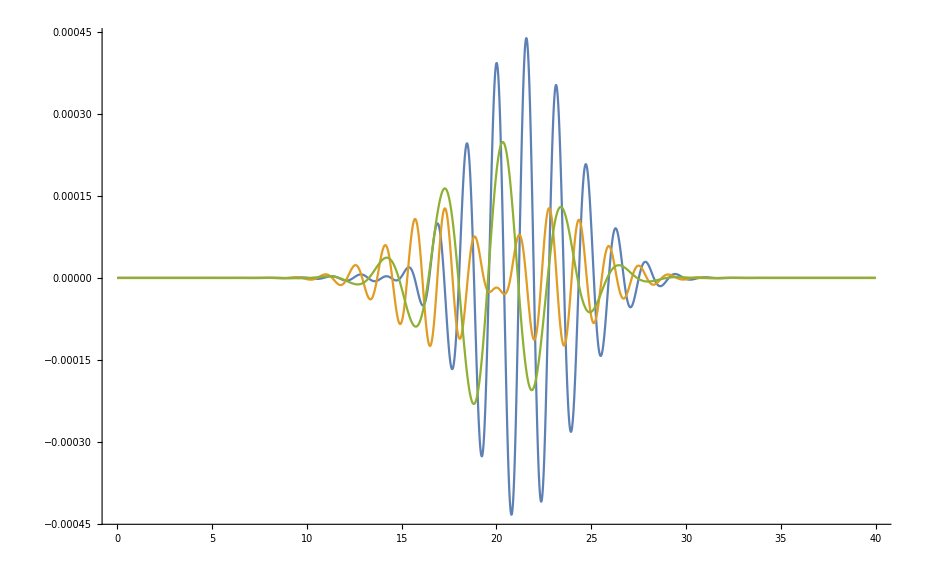

```mathematica
x0=20;
tf=x0*2;
σ=3;
Ω0=0.01;
ωr=1;
Ω[x_]:=Ω0*Exp[-(x-x0)^2/(2*σ^2)];
Gsol=NDSolve[{G'[t]-I/2*G[t]^2*Ω[t]*Exp[-4*ωr*I*t]==Ω[t]*Exp[4*ωr*I*t],G[0]==0},{G[t]},{t,0,tf}];
(**)
Plot[{Im[Evaluate[{G[t]}/.Gsol]]-0.25/ωr*Ω[t]*Sin[4*ωr*t-Sqrt[2]],Re[Evaluate[{G[t]}/.Gsol]]-0.25/ωr*Ω[t]*Sin[4*ωr*t],0.25/ωr*Ω[t]*Sin[2*ωr*t-Sqrt[2]]/10},{t,0,tf},PlotRange->All]
```

{{C0[t]→(ⅇ^(-1/2 ⅈ t (1+√(1+2 Ωa^2))) (-2 b0 (-1+ⅇ^(ⅈ t √(1+2 Ωa^2))) Ωa √(1+2 Ωa^2)+a0 (1+2 Ωa^2-√(1+2 Ωa^2)+ⅇ^(ⅈ t √(1+2 Ωa^2)) (1+2 Ωa^2+√(1+2 Ωa^2)))))/(2 (1+2 Ωa^2)),C1[t]→(ⅇ^(-1/2 ⅈ t (1+√(1+2 Ωa^2))) (-a0 (-1+ⅇ^(ⅈ t √(1+2 Ωa^2))) Ωa √(1+2 Ωa^2)+b0 (1+2 Ωa^2+√(1+2 Ωa^2)+ⅇ^(ⅈ t √(1+2 Ωa^2)) (1+2 Ωa^2-√(1+2 Ωa^2)))))/(2 (1+2 Ωa^2)),Cm1[t]→(ⅇ^(-1/2 ⅈ t (1+√(1+2 Ωa^2))) (-a0 (-1+ⅇ^(ⅈ t √(1+2 Ωa^2))) Ωa √(1+2 Ωa^2)+b0 (1+2 Ωa^2+√(1+2 Ωa^2)+ⅇ^(ⅈ t √(1+2 Ωa^2)) (1+2 Ωa^2-√(1+2 Ωa^2)))))/(2 (1+2 Ωa^2))}}

{{C1[t]→InterpolatingFunction[…][t],Cm1[t]→InterpolatingFunction[…][t],C0[t]→InterpolatingFunction[…][t]}}

(ⅇ^(-20 ⅈ (1+√(1+2 Ωa^2))) (-a0 (-1+ⅇ^(40 ⅈ √(1+2 Ωa^2))) Ωa √(1+2 Ωa^2)+b0 (1+2 Ωa^2+√(1+2 Ωa^2)+ⅇ^(40 ⅈ √(1+2 Ωa^2)) (1+2 Ωa^2-√(1+2 Ωa^2)))))/(2 (1+2 Ωa^2))

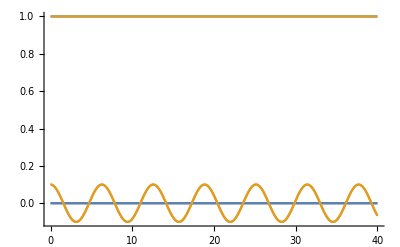

```mathematica
k=0;
sol=DSolve[{I*Cm1'[t]==Ωa/2*C0[t]+(1-k)*Cm1[t],I*C1'[t]==Ωa/2*C0[t]+(1+k)*C1[t],I*C0'[t]==Ωa/2*(C1[t]+Cm1[t]),C0[0]==a0,C1[0]==b0,Cm1[0]==b0},{C1[t],Cm1[t],C0[t]},{t,0,tf}]
soln=NDSolve[{I*Cm1'[t]==Ωa/2*C0[t]+(1-k)*Cm1[t],I*C1'[t]==Ωa/2*C0[t]+(1+k)*C1[t],I*C0'[t]==Ωa/2*(C1[t]+Cm1[t]),C0[0]==1,C1[0]==0,Cm1[0]==0}/.{Ωa->0},{C1[t],Cm1[t],C0[t]},{t,0,tf}]
y=C1[t]/.sol[[1]]/.t->tf

Plot[{Re[Evaluate[{C1[t],C0[t],Cm1[t]}/.soln/.Ωa->0]],Re[Evaluate[{C1[t],C0[t],Cm1[t]}/.sol/.{a0->1,b0->0.1,Ωa->0}]]},{t,0,tf},PlotRange->All]
```